```mathematica
Quit[]
```

#### Kernels Control

```mathematica
LaunchKernels[8]
```

URLFetch::invhttp: A requested feature, protocol or option was not found built-in in this libcurl due to a build-time decision..

{KernelObject(1,local),KernelObject(2,local),KernelObject(3,local),KernelObject(4,local),KernelObject(5,local),KernelObject(6,local),KernelObject(7,local),KernelObject(8,local)}

```mathematica
CloseKernels[Kernels[]]
```

```mathematica
Kernels[]
```

### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop]];
```

```mathematica
ParallelEvaluate[On[General::stop]];
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="~/Documents/2-d-data";}];
```

The amplitude

```mathematica
𝒞[expr_][ω1_,ω2_]:=ReplaceAll[expr,{ω1->ω2/(1+ω2-ω1),ω2->ω1/(1+ω2-ω1)}]
𝒫[expr_][ω1_,ω2_]:=ReplaceAll[expr,{ω1->(1+ω2-ω1)/ω2,ω2->1/ω2}]
ℛ[expr_][ω1_,ω2_]:=ReplaceAll[expr,{ω1->ω1/ω2,ω2->1/ω2}]
𝒮[expr_][ω1_,ω2_]:=ReplaceAll[expr,{ω1->1/ω1,ω2->(1+ω2-ω1)/ω1}]
```

```mathematica
EXPR[ω1_,ω2_][Ma_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]=Through[Through[(ℳ0+𝒫[ℳ0[ω1,ω2]]+𝒞[ℳ0[ω1,ω2]]+ℛ[ℳ0[ω1,ω2]]+𝒫[𝒞[ℳ0[ω1,ω2]][ω1,ω2]]+ℛ[𝒞[ℳ0[ω1,ω2]][ω1,ω2]]+ℛ[𝒫[ℳ0[ω1,ω2]][ω1,ω2]]+ℛ[𝒫[𝒞[ℳ0[ω1,ω2]][ω1,ω2]][ω1,ω2]]+ℳ1[Ma]+ℛ[ℳ1[Ma][ω1,ω2]])[ω1,ω2]][ϕ1,ϕ2,ϕ3,ϕ4]];
```

```mathematica
ℳ0[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=If[ω2>ω1,4 g^2 ω1 NIntegrate[1/(y ω1-ω2-x)^2 ϕ1[(ω2-ω1+x)/(ω2-ω1+1)]ϕ2[y]ϕ3[x]ϕ4[(y ω1)/ω2],{x,0,1},{y,0,1}],0]
```

```mathematica
(*𝒞[f_Symbol[arg__]]:=f[#2/(1+#2-#1),#1/(1+#2-#1)]&[arg]
𝒫[f_Symbol[arg__]]:=f[(1+#2-#1)/#2,1/#2]&[arg]*)
```

```mathematica
ℳ1[Ma_][ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=((#+𝒮[#][ω1,ω2])&[(*If[1>ω1,-4 g^2 NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,1}],0]*)
If[1>ω1,-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ NIntegrate[ω1 ω2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}]),0]])+((#+𝒞[#][ω1,ω2])&[(*If[ω2>ω1,-4 g^2 NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}],0]*)
If[1>ω1,-4 g^2(NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,x/ω1+λ,1}]-2/λ NIntegrate[ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[((x/ω1-1) ω1+ω2)/ω2],{x,0,1}]),0]])(*+((#+𝒮[#][ω1,ω2]+𝒫[#][ω1,ω2]+𝒞[#][ω1,ω2])&[If[(ω2>ω1)&&(ω1>1),-(4 π)/NcNIntegrate[(2rcp rcn+2rdp rcn+Ma^2/(x-ω1)+Ma^2/(x-1)-Ma^2/(x-ω1+ω2)-Ma^2/x)ϕ1[(x-ω1+ω2)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[(x-ω1+ω2)/ω2],{x,0,1}],0]])*)
```

```mathematica
ℳone[ω1_,ω2_][Ma_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=EXPR[ω1,ω2][Ma][ϕ1,ϕ2,ϕ3,ϕ4]
```

Solve ‘t Hooft equation

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
Nc=1000;ℂ=0;(*ℂ denotes the interchange of final states.*)λ=10^-6;g=1;
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

Used z=(r_(2-))/(r_(1-)+r_(2-)), ω=(r_(4-))/(r_(1-)+r_(2-)), ω_1=(r_(2-))/(r_(3-)), ω_2=(r_(4-))/(r_(3-)) here.

```mathematica
ωfp[z_][M1_,M2_,M3_,M4_]:=(-√((M1^2 z-M2^2 z+M2^2+M3^2 z^2-M3^2 z-M4^2 z^2+M4^2 z)^2-4 (M4^2 z^2-M4^2 z) (M1^2 (-z)+M2^2 z-M2^2))+M1^2 (-z)+M2^2 z-M2^2-M3^2 z^2+M3^2 z+M4^2 z^2-M4^2 z)/(2 (M1^2 (-z)+M2^2 z-M2^2))(*transform z to ω (Barbon), solution 1.*)
```

```mathematica
ωfn[z_][M1_,M2_,M3_,M4_]:=(√((M1^2 z-M2^2 z+M2^2+M3^2 z^2-M3^2 z-M4^2 z^2+M4^2 z)^2-4 (M4^2 z^2-M4^2 z) (M1^2 (-z)+M2^2 z-M2^2))+M1^2 (-z)+M2^2 z-M2^2-M3^2 z^2+M3^2 z+M4^2 z^2-M4^2 z)/(2 (M1^2 (-z)+M2^2 z-M2^2))(*transform z to ω (Barbon), solution 2*)
```

```mathematica
ω2p[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(-√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1)(*transform ω1 to ω2, your definition, solution 1*)
```

```mathematica
ω2n[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1);(*transform ω1 to ω2, your definition, solution 2*)
```

```mathematica
Sz[z_][M1_,M2_]:=M1^2/(1-z)+M2^2/z;(*Centre of mass energy*)
```

```mathematica
Sω1[ω1_][M1_,M2_,M3_,M4_]:=(M1^2/(1-ω1+ω2p[ω1][M1,M2,M3,M4])+M2^2/ω1)(1+ω2p[ω1][M1,M2,M3,M4]);
```

```mathematica
zfω1[ω1_][MA_,MB_,MC_,MD_]:=ω1/(1+ω2n[ω1][MA,MB,MC,MD])(*transform ω1 to z, using z=ω1/(1+ω2) and previous result of ω1 to ω2*)
ωfω1[ω1_][MA_,MB_,MC_,MD_]:=(ω2n[ω1][MA,MB,MC,MD])/(1+ω2n[ω1][MA,MB,MC,MD]);
```

```mathematica
ω1fz[z_][M1_,M2_,M3_,M4_]:=-z/(ωfp[z][M1,M2,M3,M4]-1);
ω2fz[z_][M1_,M2_,M3_,M4_]:=(-ωfp[z][M1,M2,M3,M4])/(ωfp[z][M1,M2,M3,M4]-1);(*transform z to ω1 and ω2, using z=ω1/(1+ω2) and previous result of z to ω*)
```

```mathematica
Msum[mQ_][n1_?IntegerQ,n2_?IntegerQ,n3_?IntegerQ,n4_?IntegerQ]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4,ω1,ω2,Sen},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[n1];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[n2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[n3];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[n4];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
{{M1,M2,M3,M4},ParallelTable[ω2=ω2p[ω1][M1,M2,M3,M4];Sen=√(Sω1[ω1][M1,M2,M3,M4]);If[ω2∈Reals&&Sen∈Reals,
(*Print["ω1=",ω1,"    ω2=",ω2];*)(*it's for debug purpose, you can comment this*){Sen,ℳone[ω1,ω2][M1][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω1=",ω1]],{ω1,0.003,0.5,0.01}]}
]
```

#### Calc

```mathematica
Clear["Global`g$*"]
```

```mathematica
Information["Global`g$*"]
```

```mathematica
Clear[ϕx,m2,ϕ,vals,M1,M2,M3,ϕ1,ϕ2,ϕ3];
```

#### 2→2

The total amplitude (and the square):

```mathematica
Msumdat=Msum[60][0,0,0,0]
```

Wavefunction build complete.

M1=120.335  M2=120.335  M3=120.335  M4=120.335

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.18473,3.22008×10^-6}. NIntegrate obtained -2.0144795237664044970991284981278318126552422122441064925083624007×10^3092+0. ⅈ and 9.9931950938652951738845234128477780539467313596786108828224268645×10^3090 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.210715,7.03477×10^-6}. NIntegrate obtained -3.4396718986962234206668698824836832996115518088683619190687888256×10^1927+0. ⅈ and 1.8994455590346289290690738814827890832711061711378355894319435146×10^1924 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0100804,7.03477×10^-6}. NIntegrate obtained 2.1422433393010705950119562531960793577970909494778422694281569496×10^3094+0. ⅈ and 4.7415716693975689566420206363743152616411504769467958654243772487×10^3094 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0923726,7.03477×10^-6}. NIntegrate obtained -4.8361990597929688079763928795321272190776834371274901549128315921×10^1292+0. ⅈ and 6.2041999887664580538352764991223209378853153946252029446523208408×10^1288 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0287085,0.0000261083}. NIntegrate obtained 4.6308555738691747219384599599739472677688439737231418394887871022×10^1929+0. ⅈ and 3.9791500228462277412282855602110838145038565830259030322165179972×10^1929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.7970252709377749890559277303439275344001099616784128107855839578×10^3081+0. ⅈ and 3.2370512610512914094131390412396478959138327668631788708253133319×10^3076 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -6.3631090668930647837594896046499781547625121751560109748577133204×10^1918-2.7429129853686499309756537521563681086588972247407163564257497592×10^1871 ⅈ and 1.100709404239021657457416169726723081501457520796377025152803865×10^1914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0449184,0.0000833287}. NIntegrate obtained -4.1578385908286074427926366612760913046857057479965691841265553678×10^1297+0. ⅈ and 2.5663625564683887680752540920700081489774431921184611441217348794×10^1298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.4499361346983779101661695042438212073228340790921069283959836733×10^1285+0. ⅈ and 2.1950990949339344906394918654743961807776429220493542231454607119×10^1280 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.18473,3.22008×10^-6}. NIntegrate obtained -2.0144795682938591772762569423519028611195542349829887450082436607×10^3092+0. ⅈ and 9.9931962149893907931392023038190326561527364735611794804651914278×10^3090 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.058424,3.22008×10^-6}. NIntegrate obtained -1.0975876483950196490508640097291742168737454762848045707317840297×10^1633+0. ⅈ and 3.3571578670965611856676740574916202621988582892631092620882380097×10^1628 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.210715,7.03477×10^-6}. NIntegrate obtained -3.4396718974207580364447039419916899721744885955337209683785626038×10^1927+0. ⅈ and 1.8994464715862250535285143110534833490552454701878849686506302675×10^1924 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0100804,7.03477×10^-6}. NIntegrate obtained 2.1422433093941218902850262764498618169710177189260880428313713939×10^3094+0. ⅈ and 4.7415716408574844953421002484178658309666891140447419997877727863×10^3094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0214149,0.0000680699}. NIntegrate obtained 3.2559605021669131519286692156939664525579984690717361377937105607×10^1635+0. ⅈ and 5.0829328404639444002787288679664245770164092569931052409474805312×10^1634 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.7970252708331351631709078584013768559944976686754082672487031375×10^3081-7.3012114223132992760617594489593729502324417876680766458918150082×10^3033 ⅈ and 3.2370482258042926722014525823340592430672170384678190636089211247×10^3076 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0287085,0.0000261083}. NIntegrate obtained 4.6308555633582808538817090265455279881311761617816651820951085445×10^1929+0. ⅈ and 3.9791499706165124507165633695520950828394500929273705599473588758×10^1929 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -7.5677059953042024637188207273242311496957957572384675921790363636×10^1624+0. ⅈ and 1.2549443210993575457152138509858317638520816020833418943449155898×10^1620 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -6.3631090668933117561638641277758632127412683713633154843832194225×10^1918-2.7429129853686493664467509025324027356903037569995096421726176079×10^1871 ⅈ and 1.1007094017631686132749869642096467701755226103037281860399054207×10^1914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0923726,7.03477×10^-6}. NIntegrate obtained -4.8361990596397673584488777289970731917429624890312297995395890133×10^1292+0. ⅈ and 6.204201254125539755475316060668019757857649497526231499300905719×10^1288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0449184,0.0000833287}. NIntegrate obtained -4.1578385906800176794800464305051200676026120430180277907183575351×10^1297+0. ⅈ and 2.5663625564378589433514025382948987553253355901145312727237588473×10^1298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0958762,3.22008×10^-6}. NIntegrate obtained -1.3097496194031971195100579048172204690159789305697959279180466386×10^1492+0. ⅈ and 2.555875447836774085925586509969669976875325645135368151815621466×10^1487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.4499361347201112824264786350131565583971679873427805362722174929×10^1285+0. ⅈ and 2.1950981272120091061428265621500096320679917620144230640441658155×10^1280 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0239382,0.0000871434}. NIntegrate obtained 3.1560085354681491158954168779961046338001420796651196184385315994×10^1495+0. ⅈ and 6.9180680258087829557148651781511522361463028399799811303595136212×10^1495 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in y near {x,y} = {0.210715,1.61004×10^-6}. NIntegrate obtained -2.4020214933991029443274006428733265001718793296603762334201848192×10^2453+0. ⅈ and 3.3047143608875846034501078387843718348199030892054093540231138554×10^2450 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,7.03477×10^-6}. NIntegrate obtained -4.8432781877269918227557577339971816375279378462355821140734886222×10^1215+0. ⅈ and 1.4294947404720981534401326850103349714800886085978040904619988117×10^1210 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0856866,7.03477×10^-6}. NIntegrate obtained 1.7518237142944991969280647381454349541891753655488370451513444373×10^2456+0. ⅈ and 2.4901858991149291486428714227056807302043849575198843227380570281×10^2455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -4.0603155497830433260569002191485660293466951530221510996100280093×10^2443+0. ⅈ and 7.2470201051588552919282047186538364359751568231965601534638407828×10^2438 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0240415,0.000171067}. NIntegrate obtained 2.7311967867014920897794391623348801332120521031496177658228840323×10^1218+0. ⅈ and 1.9218873854292686026164033101913634000070316799902122227663403692×10^1218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.058424,3.22008×10^-6}. NIntegrate obtained -1.0975876482733067658728267834968609877486604172937844210464740236×10^1633+0. ⅈ and 3.3571572535358827281355242689948676958596409283701997774834321046×10^1628 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.9998796353406737543295298886203430646450900863064816373115034616×10^1208+0. ⅈ and 2.9462562525026219806989789500581369015462935235591070068006525305×10^1203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0214149,0.0000680699}. NIntegrate obtained 3.2559615705572965176061955814142897656082535587004038204367066278×10^1635+0. ⅈ and 5.0829343084591910845827986301078800909929801242554494027705668954×10^1634 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in y near {x,y} = {0.210715,1.61004×10^-6}. NIntegrate obtained -2.4020214748366467721701887249939998617543541300131490125100305251×10^2453+0. ⅈ and 3.3047129599973368323067869022239679781471442570252884795386833099×10^2450 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0341575,0.0000108495}. NIntegrate obtained -5.3778710350718742603125448677359403816948004706688148655563138466×10^1382+0. ⅈ and 2.1440885008074785663877582945691287191289295574792138285781858661×10^1377 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -7.5677059952634834973009175345323327916149041239434420612465393007×10^1624-3.4800894941154568006273505825263021986842788636387267190607044318×10^1577 ⅈ and 1.2549433818441459184104834099280862587791349854809696483268537268×10^1620 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.146508,3.22008×10^-6}. NIntegrate obtained -3.5347555532918958868046067459745707935994498221440849060592524115×10^1834+0. ⅈ and 1.1305602293895560175019728020949673079797263150663039121650125386×10^1830 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0856866,7.03477×10^-6}. NIntegrate obtained 1.751828724662286769495350199145986784074774871882249793581426192×10^2456+0. ⅈ and 2.4901929290087208091519035780116670736519180717591369267244587328×10^2455 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0285484,0.000102402}. NIntegrate obtained 1.5428919645432548377113016405959168355531655972012062040332186839×10^1385+0. ⅈ and 4.495735866372810185077433877415346604745214391455833777207594678×10^1384 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0856866,0.0000146642}. NIntegrate obtained 2.6588733975082154471280207427213976593756433083633933474139200383×10^1836+0. ⅈ and 9.6905865632373675092605204595449273493576872944826873702172857147×10^1835 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -4.0603155495451814627685195581274665721395962466733472382339610511×10^2443-1.6716663348938914702514657916399143080087862584475961830576231839×10^2396 ⅈ and 7.2470131307322337059015740216607137165780037078858501906967883546×10^2438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.101287749226979877991292146298461383991334842279109430581459637×10^1375+0. ⅈ and 1.7167542234976065590258970405746323620106361474933079904463570434×10^1370 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -9.9346933186856078958482308865665310795069090777618347194508268156×10^1825-4.351021256123650225808935637105373059923582060331481726631611801×10^1778 ⅈ and 1.7004498875012206831946917000636413620503372237470528759183538145×10^1821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0958762,3.22008×10^-6}. NIntegrate obtained -6.1259766291043564955196770367986658745279814008361479250275179576×10^1265+0. ⅈ and 7.5687324381894100073548503552417740532951427634084928748172167578×10^1260 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,0.0000146642}. NIntegrate obtained -1.1293815892888525937185395837729061679814141380849789147354927933×10^1148+0. ⅈ and 2.1280226183162113433981907397374721500813127638755571994811942931×10^1142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in y near {x,y} = {0.0752084,0.0000531085}. NIntegrate obtained 1.8965354687604602187535757059552024045194546211857172735734560679×10^1268+0. ⅈ and 2.4857063960337534886295463664714108876569795923601350570865606197×10^1268 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0923726,7.03477×10^-6}. NIntegrate obtained -2.2446235169353345664328449942002378333495838890924751672021806648×10^1581+0. ⅈ and 4.6297882281254375149548032826670443762678263405360155249023475693×10^1577 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,0.0000718846}. NIntegrate obtained 9.7993299467233205243795563362537184761136488853551819466547724083×10^1149+0. ⅈ and 7.8585687002663624910812845809991633895912936169475662326967979571×10^1150 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.0552496808727352749247666867560184453093561640834673323517868934×10^1258+0. ⅈ and 3.0828142757251059422041655212619001056540343125034716805158772914×10^1253 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -6.14546457559527657776145838286597866340588333358227424397258919×10^1140+0. ⅈ and 8.8262029081214956409571273042776036898653931489163234243046116883×10^1135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0121886,0.000144364}. NIntegrate obtained 4.5595778684693877821155386002523669175011086095075802115228633634×10^1583+0. ⅈ and 7.8328860417577107036484116911316924053078807617186814261620855505×10^1583 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0958762,3.22008×10^-6}. NIntegrate obtained -1.3097496201886518248109363218368234001954998005122257468646491146×10^1492+0. ⅈ and 2.5558783964291857604733863573368823308172890597981888870839367702×10^1487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.9432368048305732638476536683769234965279114552037188914743527233×10^1573+0. ⅈ and 3.188838125415187742585715969739458704545435201886383385017930212×10^1568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0239382,0.0000871434}. NIntegrate obtained 3.1560085345202275551535010326179974832753081779811438839980938946×10^1495+0. ⅈ and 6.9180680295778915366502105746660343689679330184899505344904432876×10^1495 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0326962,3.22008×10^-6}. NIntegrate obtained -3.4245971743674113079646042339521344989200439247209226273215796384×10^2203+0. ⅈ and 6.2144823038410086172181301117400111600165309046663216684853567708×10^2199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0262618,0.0000146642}. NIntegrate obtained 2.6372766276011341116609346959661178728177699142748179437667843991×10^2205+0. ⅈ and 5.4365569100427471468396383103232957678400543462191997639672136528×10^2204 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.146508,3.22008×10^-6}. NIntegrate obtained -3.5347555523981322743080704260531957849692515123473486437535272663×10^1834+0. ⅈ and 1.1305496860999251614646197717819018702905157790812576003370403441×10^1830 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0923726,7.03477×10^-6}. NIntegrate obtained -2.2446235201096999673049831414783305851190596030253802668962356077×10^1581+0. ⅈ and 4.6297875056132370225782249754526214522701169157391924567105719259×10^1577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.8120955067629610845948862722962511676660312936734680068048867147×10^2194-7.5726278100581517505514998658465011645305791543241667440764473446×10^2146 ⅈ and 3.2012600035977919616953165379931148619552048026694669773418016645×10^2189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0856866,0.0000146642}. NIntegrate obtained 2.6588733237279680200585413969089555101021175093990321383042597949×10^1836+0. ⅈ and 9.6905867020890614121179547133379851089364263790112655590424683055×10^1835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0121886,0.000144364}. NIntegrate obtained 4.5595698306494951249024115866668820561676395139417941812389863152×10^1583+0. ⅈ and 7.8328642299378914467889082615452452129883412000230966181889779188×10^1583 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -9.9346933191536820400811519218897035034635733227655157438576654111×10^1825+0. ⅈ and 1.7004500665073798024204620736830214187448458592827999462874278945×10^1821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.9432368048307299295557897233298323117648400245225617518861457548×10^1573+0. ⅈ and 3.1888381281620967540111719039258054304858458043224663343424518635×10^1568 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,7.03477×10^-6}. NIntegrate obtained -4.843278188456196468759809697566328375862775587475882223687678785×10^1215+0. ⅈ and 1.4294984711247365439230059491642537086914493589755831334874403492×10^1210 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0240415,0.000171067}. NIntegrate obtained 2.7312004562394808874207051723662651753438923037989231508619300682×10^1218+0. ⅈ and 1.9218959912801966139813051587157626048193759440865420716843234049×10^1218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.9998796353403388118305204615989438662019737001620473057242863409×10^1208+0. ⅈ and 2.94625625554065040136544280121836917399231134697079852608475369×10^1203 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0958762,3.22008×10^-6}. NIntegrate obtained -6.1259766292176053371046380570645318958768672940162642976792339068×10^1265+0. ⅈ and 7.5687265118741065186187649791954543759338942649121625193059171529×10^1260 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0923726,3.22008×10^-6}. NIntegrate obtained -8.6493257430979711793605731722532386344217768213278166563307455082×10^1452+0. ⅈ and 1.7262635881754723652690309387671726436093902168998403506244603245×10^1449 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0326962,3.22008×10^-6}. NIntegrate obtained -3.4245971832141555990381827956594436558420059550935800291323188947×10^2203+0. ⅈ and 6.2144972298747955306287672067641558159041723321932647104205524142×10^2199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in y near {x,y} = {0.0752084,0.0000531085}. NIntegrate obtained 1.8965354688010776517939205228384221992290349994065952379269130273×10^1268+0. ⅈ and 2.485706396215504069926301323336039204349093066632874679093112328×10^1268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.0552496808728337547869098844556698355244665303045994112532832886×10^1258+0. ⅈ and 3.0828142740903527548640314251939570998570664805359694244087132745×10^1253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0923726,7.03477×10^-6}. NIntegrate obtained -1.8804122683849474018264941369996249915891002478972933606057767609×10^1757+0. ⅈ and 4.3791309332361939416262188486562391442861102036140294588584644844×10^1753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0262618,0.0000146642}. NIntegrate obtained 2.6372766623388858462764615806984989328542931708866928742294460202×10^2205+0. ⅈ and 5.4365573052402564062051126286399855005987828608685555700220549751×10^2204 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.022294,0.000102402}. NIntegrate obtained 4.3262857432904111434710610715110919113855546809889167261806892156×10^1455+0. ⅈ and 7.1738185344066995922070624585121300115021566586595570222410482774×10^1455 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0923726,3.22008×10^-6}. NIntegrate obtained -4.88790176391476890162649623803633146104816832966934946553782804×10^1534+0. ⅈ and 1.178717427554456950689167328359720909986888209560490755436638766×10^1531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.3101821123181012689753800291064497815234010117140105812133108501×10^1445+0. ⅈ and 2.0842256658190917971183010337932617746042248817890552887402826761×10^1440 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.812095506763091253490160677313266335570338384628083069273727773×10^2194-7.5726278100581474905212887798635019591512078529408807799360611463×10^2146 ⅈ and 3.2012599996076223242485923274245728850874371971285258836798598255×10^2189 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0226737,0.0000528111}. NIntegrate obtained 3.6850072499200463990872167838486923687916341030110291497305619181×10^1759+0. ⅈ and 4.5435796581132185994292498789725635202823710505456864710664618529×10^1759 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0246924,0.000079514}. NIntegrate obtained 2.3932576641197104387121616595816927413102086896941412280755648099×10^1537+0. ⅈ and 3.9110923206879646917811093456080717867424360715692248957578823972×10^1536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -7.4682773157849176436337847947664270886694415405708390950609167277×10^1748+0. ⅈ and 1.2648452250959422344128490842956596378942269000344096532807893321×10^1744 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -5.1910456250655301205891674741050048148645909796409922842087983758×10^1526+0. ⅈ and 8.4301039010719214494193742028809056357672791859151947900891154179×10^1521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0341575,0.0000108495}. NIntegrate obtained -5.3778710348328308240635118008902137158560845019540470939243984874×10^1382+0. ⅈ and 2.1440844181728130875958824345960613412882442692428357954300305638×10^1377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0285484,0.000102402}. NIntegrate obtained 1.5428918267830943831180933664033975967272986002068282351992756446×10^1385+0. ⅈ and 4.4957391378845995007300768015975900976282359965371682250624869832×10^1384 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.210715,3.22008×10^-6}. NIntegrate obtained -4.3571726807300800789180715647680389485891810727657503726350871127×10^2044+0. ⅈ and 4.1857136726745466442452059127058230074022134589606281132874822472×10^2041 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0923726,3.22008×10^-6}. NIntegrate obtained -8.6493257430979711793605731722532386344217768213278166563307455082×10^1452+0. ⅈ and 1.7262635881754723652690309387671726436093902168998403506244603245×10^1449 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0923726,7.03477×10^-6}. NIntegrate obtained -1.8804122679155972444341987567512613796092527294398461432955791263×10^1757+0. ⅈ and 4.3791360060412417069324355152568325235274970037726356039238965851×10^1753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0923726,3.22008×10^-6}. NIntegrate obtained -4.88790176391476890162649623803633146104816832966934946553782804×10^1534+0. ⅈ and 1.178717427554456950689167328359720909986888209560490755436638766×10^1531 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.1012877492443212960529301314540468917832960382174920526371313675×10^1375+0. ⅈ and 1.7167535117147303031325913526962188077154729965668675423263867859×10^1370 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0326962,0.0000222936}. NIntegrate obtained 3.3339839424330141713830141610144845831229715609042867054276389228×10^2047+0. ⅈ and 7.249553995509295372943563409068760592087737470693671286738275377×10^2047 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0226737,0.0000528111}. NIntegrate obtained 3.6850072534081731479289397602764133939307422277672221321139082004×10^1759+0. ⅈ and 4.5435796548738077776305680075120109962723950671517310358350292195×10^1759 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0246924,0.000079514}. NIntegrate obtained 2.3932576641197104387121616595816927413102086896941412280755648099×10^1537+0. ⅈ and 3.9110923206879646917811093456080717867424360715692248957578823972×10^1536 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.022294,0.000102402}. NIntegrate obtained 4.3262857432904111434710610715110919113855546809889167261806892156×10^1455+0. ⅈ and 7.1738185344066995922070624585121300115021566586595570222410482774×10^1455 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -7.4682773156415914736839126793284420704452921015934471734373079084×10^1748-3.3238219806127452926555704334246388804912949084096465834959754633×10^1701 ⅈ and 1.2648441769012786880571071554981745265292773288625671655779995982×10^1744 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -4.7473452319421752373664948475960083536355422066477946486960347539×10^2035-2.0146283920361105499539755840508456837411060742316688383431899519×10^1988 ⅈ and 8.2992344918461961336155877206762783819087378199120633415859863215×10^2030 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -5.1910456250655301205891674741050048148645909796409922842087983758×10^1526+0. ⅈ and 8.4301039010719214494193742028809056357672791859151947900891154179×10^1521 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.3101821123181012689753800291064497815234010117140105812133108501×10^1445+0. ⅈ and 2.0842256658190917971183010337932617746042248817890552887402826761×10^1440 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.210715,3.22008×10^-6}. NIntegrate obtained -4.3571726844049087041659035261711693165321458596748396140429863082×10^2044+0. ⅈ and 4.1857107043351590464858874118748202925299123561138742434855057968×10^2041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,0.0000146642}. NIntegrate obtained -1.1293815894280691842633050075130274107925363424347130506097416342×10^1148+0. ⅈ and 2.1279954269189836874760565589232264887516041986011749540614718828×10^1142 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0326962,0.0000222936}. NIntegrate obtained 3.3339839417675817738180688449449422472932670015424695321253516643×10^2047+0. ⅈ and 7.2495539980375504891940665863484274947080993891859832503495145054×10^2047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0923726,3.22008×10^-6}. NIntegrate obtained -1.1381308676486202304038568751843094315546193799841239651010598514×10^1691+0. ⅈ and 3.4318574004236640772899491743431445605563136433197873731034036975×10^1687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -4.7473452321645461445612278953521379647038162594140162491831885439×10^2035+0. ⅈ and 8.2992351555072794011462166762008200837180062297966796217864345095×10^2030 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,0.0000718846}. NIntegrate obtained 9.7993300649390530039758271315000871611821034404481029249545118172×10^1149+0. ⅈ and 7.8585687020061025811289349016254084221201870687340580921948483837×10^1150 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -6.145464575509784119790928953659841122878087487055405628797804584×10^1140+0. ⅈ and 8.8262073334949297809773599101471499526132309230366990222647972671×10^1135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0157685,0.0000833287}. NIntegrate obtained 1.4251925735075013047767893285120161289788323478751584792106009988×10^1693+0. ⅈ and 5.7920103530797533883330626802106934095403575710480056159655023581×10^1692 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0923726,7.03477×10^-6}. NIntegrate obtained -4.1126237307192386933081804646116035991544950963718645467398096709×10^1416+0. ⅈ and 6.5228209076158937484360050615763724313002357008603146554517700569×10^1412 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -6.0700226197693417451241284019698535911151423146740556805315523919×10^1682+0. ⅈ and 1.0172349282180404842088496409484904990559197238336570003008230963×10^1678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0856866,0.000041367}. NIntegrate obtained 2.5843482977241631245317998909912723903685746047130684806626757576×10^1419+0. ⅈ and 3.4085672957873666039222105399068856427180019377792464249704876272×10^1419 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,7.03477×10^-6}. NIntegrate obtained -1.4608179171560096984117569184835873975271123720555353391089617027×10^1240+0. ⅈ and 4.5881092475969181728660768831347556753924241943758811786316954722×10^1234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -7.2849730122713752151766892589250079818794068529337150551122125896×10^1408+0. ⅈ and 1.1471368657150797774544415159001327165511696534337460491316201083×10^1404 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,0.0000146642}. NIntegrate obtained -1.7222274525244419903370829970236870111272537514131995370280025843×10^1192+0. ⅈ and 3.2882303688897315129302691291269219284691798679336247602428718251×10^1186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in y near {x,y} = {0.0226737,0.000178993}. NIntegrate obtained 2.127583886739864021188008593326339077452708960434677323575946354×10^1243+0. ⅈ and 3.4710410478015882462869947868812793218619906488559025034870551836×10^1243 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0923726,3.22008×10^-6}. NIntegrate obtained -1.138130867686672086782063029228171075378075534840382366005880593×10^1691+0. ⅈ and 3.4318573312348773507555725795969141099490866223840614001908917609×10^1687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -5.4518034169606624816879078918745220320185919264880196283310055829×10^1232+0. ⅈ and 8.1035331247994624398340631682287415574966974293934578254375649214×10^1227 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0343598,0.000129105}. NIntegrate obtained 2.3218859341803661672841135032464842755237531437066148663911753307×10^1195+0. ⅈ and 4.8976871942457746093794600919509263835848234105706019105812476609×10^1195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0958762,3.22008×10^-6}. NIntegrate obtained -8.9765831851257511335886751208544210381671122152763980597647251707×10^1350+0. ⅈ and 1.2947648449923720652530249832781246598172777530733788167175825607×10^1346 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -7.8300562623981153111009537380328594596251526057018947518560255866×10^1184+0. ⅈ and 1.1435375355040916419389564378656848297872490874868306742053802057×10^1180 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0157685,0.0000833287}. NIntegrate obtained 1.4251925723767529870398972482078787171304424723061980212197336048×10^1693+0. ⅈ and 5.7920103788648236537114697465079919570044203426689554306198623808×10^1692 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0229374,0.000129105}. NIntegrate obtained 3.1612308450491606413657952305841957151932620130952090471920941392×10^1354+0. ⅈ and 7.2407693326345996404946632329462597603599646213639168963765009894×10^1354 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -6.0700226197694716562173400291295433460149379716170697149684114639×10^1682+0. ⅈ and 1.017234927504987852989836625967773963264097371165770535845951373×10^1678 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.1045262430964179620932335618308361616767762600558020856153621315×10^1343+0. ⅈ and 3.2481229893186219293836714267266001974511491823164945727272259973×10^1338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0923726,7.03477×10^-6}. NIntegrate obtained -4.1126237298986000028462020546131387177213202838913984054372953028×10^1416+0. ⅈ and 6.5228212771016518974650365866685293624459466911777353809930220561×10^1412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0856866,0.000041367}. NIntegrate obtained 2.5843481066455576406611775599110645511731929771987950413392321346×10^1419+0. ⅈ and 3.4085671071151775844200232098688173280733000553345392143775990567×10^1419 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -7.2849730122710513141985861593429943327315079719822587211796201658×10^1408+0. ⅈ and 1.1471368643101202050218241571482808026614069175930419362133534555×10^1404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,0.0000108495}. NIntegrate obtained -2.7901751211026832398052094962243734071228301209740557562386033675×10^1087+0. ⅈ and 5.2222181778854337470829001582560099693621014722573560561617578894×10^1081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0303236,0.00019777}. NIntegrate obtained 2.1735276050046978753129215828811835271577689486328562974423085148×10^1092+0. ⅈ and 3.0689714428517478526237453004009784578630841130345679907361345438×10^1091 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.9349883539457336395000978227406503316993185584785633728389981248×10^1080-1.2400657225171015607977106629331031551188099402459939792779457323×10^1033 ⅈ and 2.730241203958594497639478069205184757979385002339394307574039815×10^1075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0958762,3.22008×10^-6}. NIntegrate obtained -8.9765831848118654850144766785105629752406641986044297516328579124×10^1350+0. ⅈ and 1.294764746001106990429562955050176777693313758998195124248955219×10^1346 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,7.03477×10^-6}. NIntegrate obtained -1.4608179171560096984117569184835873975271123720555353391089617027×10^1240+0. ⅈ and 4.5881092475969181728660768831347556753924241943758811786316954722×10^1234 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0958762,0.0000489964}. NIntegrate obtained -1.8935406458834056140612621058588768405022917416016195361363474315×10^1032+0. ⅈ and 5.333079107192956958337501341512786777092490184811751571180465972×10^1026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0229374,0.000129105}. NIntegrate obtained 3.161230844936747472564593872828954840230037939981512395859489446×10^1354+0. ⅈ and 7.2407693323738735697575545349669808979414051190507272439193939849×10^1354 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in y near {x,y} = {0.0226737,0.000178993}. NIntegrate obtained 2.127583886739864021188008593326339077452708960434677323575946354×10^1243+0. ⅈ and 3.4710410478015882462869947868812793218619906488559025034870551836×10^1243 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.1045262430793629561806332354515376020294856967283223586942362207×10^1343+0. ⅈ and 3.2481201766234537520184010801910043665595510988320367183971511187×10^1338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -5.4518034169606624816879078918745220320185919264880196283310055829×10^1232+0. ⅈ and 8.1035331247994624398340631682287415574966974293934578254375649214×10^1227 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0113982,0.000586869}. NIntegrate obtained 2.2329114949512782354272344798483469160785041038064747279671197411×10^1034+0. ⅈ and 4.5249519441383067137563896665080931133308502662781771293067047902×10^1033 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.6303546992685665665604561724580551101561486728338002634335719016×10^1025+0. ⅈ and 2.3904940372160025599888484053770276787333753259148001210502579028×10^1020 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,0.0000146642}. NIntegrate obtained -1.7222274518974714908761488730664304739852964297460353835253580898×10^1192+0. ⅈ and 3.2882198393081877448609897902575531109450932360048870607819881355×10^1186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0343598,0.000129105}. NIntegrate obtained 2.3218962239449781344274022021682521370436726161828928856619565395×10^1195+0. ⅈ and 4.8977119466777961225915628570111961695275418558658694218787730561×10^1195 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -7.8300562623961202768876964728941361147037180632917438244321232543×10^1184+0. ⅈ and 1.1435375332163716054692320428196056567490084921698661200345896503×10^1180 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0249048,0.000312211}. NIntegrate obtained 8.3472508019669651937991984145341784634906832129032463718203187845×10^983+0. ⅈ and 1.4223160311799649391952344374215154732246947865299587773157584556×10^983 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.7562900778404482378622272783395740242967046319559424984027870395×10^974+0. ⅈ and 4.193645881563058160381314296239822793606271256235814964259925114×10^969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.058424,0.0000985875}. NIntegrate obtained 6.5899559289377065312997709402283397256091032458588517961196889599×10^1130+0. ⅈ and 1.3911042118962022080009660155389115498538252018980813482332785803×10^1131 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -8.5581863193052086343705403467224483905877260300635913738465803863×10^1119-5.2660785961394399704059578468411666045023851023574341815068923485×10^1072 ⅈ and 1.2193552605893034978825382682930651519615993241792167681234677737×10^1115 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,0.0000108495}. NIntegrate obtained -2.7901751213149380530478828912516137305857985911001804478970024043×10^1087+0. ⅈ and 5.2222798003361726636254892976033961070931621941199614431677525993×10^1081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,3.22008×10^-6}. NIntegrate obtained -1.1028469457339159004174739805038008888634675514752974903363080222×10^934+0. ⅈ and 1.4040784539612266671664697179150479661129510247587262237459710375×10^928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0303236,0.00019777}. NIntegrate obtained 2.173527605155668749770531758491367768802497570730403947030843593×10^1092+0. ⅈ and 3.068971448620427902769114104813726139566362808378934126709250771×10^1091 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0326962,0.000327469}. NIntegrate obtained 3.4510855457602298483289345891330247746270508133747716564679722962×10^935+0. ⅈ and 2.9138230150544860400708363834778093921941045255989724627830498376×10^937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.9349883539839226169411319114801943456211321631535685484514663353×10^1080+0. ⅈ and 2.7302429418097078402604953862651361619084948643190020022193611852×10^1075 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.3791873636861805644873608137819652438546805635203510921227756997×10^927+0. ⅈ and 2.174215174448503897753384515570516617592369143812774269883638206×10^922 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0958762,0.0000489964}. NIntegrate obtained -1.8935406463125759349566360177758366884737811728470249207943656145×10^1032+0. ⅈ and 5.3330663948932798048592567810403242472895573389286256108673941062×10^1026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0341575,0.0000146642}. NIntegrate obtained -1.027246400189344154640502078594449642291264675634229656168621115×10^1321+0. ⅈ and 3.435136990823910594136749761229725419630435087904176448219515559×10^1315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0113982,0.000586869}. NIntegrate obtained 2.2329096594800582726278036568536966198700632467223639265974677769×10^1034+0. ⅈ and 4.5249453088657133126985225727084475750584520736052802015969688233×10^1033 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0444805,0.000228287}. NIntegrate obtained 3.1057517660749621033066768889138280109581104339747135263779511254×10^892+0. ⅈ and 7.8740373480821344829234045003999483962707297361646789250171125863×10^891 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0101186,0.000308396}. NIntegrate obtained 5.313074234757717688638081273180515423629429619519423349658658519×10^1322+0. ⅈ and 1.8772781589367437974241820890412952831982648640530159780850098285×10^1322 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.6303546992152692710867725534007884107620679790286804530344483155×10^1025-1.1128989474351242102218936267294448973407749904134292896372626564×10^978 ⅈ and 2.3904901941984145503958831458495477890620408750011045478308004337×10^1020 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -4.7391300458230348274639988901202664135414439275222159721962249164×10^882+0. ⅈ and 7.7288477590074665556961302972569940763597038663187401034839756476×10^877 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.733707143300094859836324321291492432617323013662023596953984903×10^1313+0. ⅈ and 4.1778881021976763352217197010577032099480298026578397568825337293×10^1308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,0.0000184789}. NIntegrate obtained -5.2501773856828472783655660336590266776035277115880987112712450619×10^1169+0. ⅈ and 7.6218215495881562925493174784565297050154271349274644924614275684×10^1163 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0225348,0.000205399}. NIntegrate obtained 5.4246713037762623275810037635569580522748934708724101926014677659×10^1172+0. ⅈ and 7.5722383417764955784511200048265929242343330066029331541134726816×10^1172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.6166291014459921095688642609137117041842908478903120683401220131×10^1162-1.5475549500905176982017240994632456646175580382806575764595252441×10^1115 ⅈ and 3.7891558590934869328595425116874443301571922850594869661972307718×10^1157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0249048,0.000312211}. NIntegrate obtained 8.3472502778790110447140764216834834931627302503368841898653798587×10^983+0. ⅈ and 1.4223158540753564755041742564948661662117261402095043047347022941×10^983 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.756290077796900224510749922229728552709588174287857297879846863×10^974+0. ⅈ and 4.1936433003089286407126993145077971240201535780339326878953196608×10^969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,0.0000146642}. NIntegrate obtained -3.2734700396310077328404222139620045986784157439213304132868994655×10^1068+0. ⅈ and 4.8028393550496855722014075527368272575031339713380766691880353939×10^1062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.025758,0.000239731}. NIntegrate obtained 2.193295257141343245539300825224196264197957926497459196762710084×10^1072+0. ⅈ and 1.2534402035223996522246831505990275954893955489227374905987332393×10^1072 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,3.22008×10^-6}. NIntegrate obtained -1.1028469457246563428909360494441764088933252193699867904647304587×10^934+0. ⅈ and 1.4040760564703045867023272962228660051524819078556971321658561282×10^928 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.4463253894667098059930327161472831114454569336292606726016561468×10^1061-1.6006295978065331306105671039268011903858159489745389456067928956×10^1014 ⅈ and 3.4967529619758889528913301016762239871509119766856137240507481692×10^1056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0326962,0.000327469}. NIntegrate obtained 3.4510855454508716206578206149016136130455697543490396754772872697×10^935+0. ⅈ and 2.9138230152767617570932572117924539116945441674651040232977051924×10^937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.3791873636347557784752153644489844914970960904362130375170393768×10^927-1.0771344455062859352542868650785381710303751978482868357189123938×10^880 ⅈ and 2.1742116384210158003425978744376009122758576771921156694511896794×10^922 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.058424,0.0000985875}. NIntegrate obtained 6.589944386323278798663379382414202174682644199227616305299369877×10^1130+0. ⅈ and 1.3911015661833476381049057129044901968371653596955061480138308768×10^1131 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0341575,0.0000146642}. NIntegrate obtained -1.027246400189344154640502078594449642291264675634229656168621115×10^1321+0. ⅈ and 3.435136990823910594136749761229725419630435087904176448219515559×10^1315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -8.5581863197425629631150571184127515202419784729124344372264777539×10^1119+0. ⅈ and 1.2193556716864584049936799451889458944474645025766262605053378506×10^1115 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0444805,0.000228287}. NIntegrate obtained 3.1057448598151779815896011456890164689347825490152875101382414097×10^892+0. ⅈ and 7.8740244143260263519942989326809602044277533715981520864696087455×10^891 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0101186,0.000308396}. NIntegrate obtained 5.313074234757717688638081273180515423629429619519423349658658519×10^1322+0. ⅈ and 1.8772781589367437974241820890412952831982648640530159780850098285×10^1322 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -4.7391300455643348892522355625669740490155731675600159023648058443×10^882-3.9777755065971009232194740980440849724996948133689659788984996832×10^835 ⅈ and 7.7288312488271185823897790430931212380375115837707566351023913×10^877 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.733707143300094859836324321291492432617323013662023596953984903×10^1313+0. ⅈ and 4.1778881021976763352217197010577032099480298026578397568825337293×10^1308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0958762,0.0000337377}. NIntegrate obtained -1.8882615981361201357721077378472672295642360537447505354863251008×10^965+0. ⅈ and 5.7192366672393683030630173796271440611296200726796703057914348588×10^959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0258679,0.000312211}. NIntegrate obtained 1.5290965039421387097665590979258369459074717880640253337191808609×10^968+0. ⅈ and 7.1170389335833632118362803761763838197556153545061071608600248915×10^967 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.1009302021866325834120612401558614739515021172626610915338579516×10^958+0. ⅈ and 3.2351109789454859724995398502026835235820113343416201431934788071×10^953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0225348,0.000205399}. NIntegrate obtained 5.4246449248667044709329880436086603319824345675328152852753594909×10^1172+0. ⅈ and 7.5721821477557078918131101768934472772386200565298546896621085715×10^1172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0110265,0.00063646}. NIntegrate obtained 1.825757812717844101337411389536900303166635357855444815274422595×10^1017+0. ⅈ and 3.2863541085657195553659890460484676981412027160401820537729030635×10^1017 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.6166291015786904923061081264276022366518986185126537348157307286×10^1162+0. ⅈ and 3.7891570327304036567396104663044764050114011494873868636269380882×10^1157 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -7.1812966128619998042299785318677390876444583902930160880909459838×10^1007+0. ⅈ and 1.0661837708376551206044635971655510916093615024174786439947870955×10^1003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,0.0000146642}. NIntegrate obtained -3.2734700386798709555969665358736495291181962681960623713966188349×10^1068+0. ⅈ and 4.8029753755149345267976941233722477833886969847526600234227758746×10^1062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.025758,0.000239731}. NIntegrate obtained 2.1932849830574196364600659290817821051882325703080118352297999046×10^1072+0. ⅈ and 1.2534300682318587712707002606094759409038132058451861108746980653×10^1072 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.446325389543115536553627580445620319022198602598108186392046748×10^1061+0. ⅈ and 3.4967585813350773872958952926490498496722137934576120522452065978×10^1056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0958762,0.0000337377}. NIntegrate obtained -1.8882615982377098778606406532956268545252898275989104016206043098×10^965+0. ⅈ and 5.7192367152318004980690473254673259675583740468819054695016516644×10^959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0258679,0.000312211}. NIntegrate obtained 1.5290964810528250674361319831521599709716692613982255990420517767×10^968+0. ⅈ and 7.1170388977894771813233996134831856954954776261736817860967639309×10^967 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.1009302021115827918079339728612709911805006223193156098992443354×10^958-1.5667073515285613732069497558093525776676507440302552214024137632×10^911 ⅈ and 3.2351057403863459184373304511214198769618617424994755749239708719×10^953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0293497,0.000354172}. NIntegrate obtained 8.8482653343233963287439040107284782093883627536106219604237595221×10^877+0. ⅈ and 1.8358437101780609237872324596057690565543487604243477162901028576×10^877 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.4863581473410124522715097705143315623402074735967929528993616095×10^868+0. ⅈ and 4.0995674711713105655491038407528001685603105437613390237271714896×10^863 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0262618,0.000365616}. NIntegrate obtained 3.3956878950850942834036760837118297959407158860122387028200299169×10^921+0. ⅈ and 7.2146923089429548214438147832345696594711077753511774603105978708×10^920 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0958762,0.0000756993}. NIntegrate obtained -9.4824946743910197745439250946256330963989581968556965351405900218×10^1106+0. ⅈ and 2.0233548218783177471068473005622467017412603157271146652532501987×10^1101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.0717200029549398254862488658257319814042931081335567511548928018×10^912+0. ⅈ and 1.7090269517008771537523134229831605320280879820964963362446625342×10^907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0352896,0.000159623}. NIntegrate obtained 6.5620108480240539259883343418607885925389888707988849759156059151×10^1109+0. ⅈ and 1.0242390509602106125183873719363497305426673791638197734560064843×10^1110 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -6.0849123434086406748287961165372748830040959388365104560246088147×10^1099+0. ⅈ and 8.6030659556401552933401128268826151170532004242995320267836121781×10^1094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0330871,0.000346543}. NIntegrate obtained 4.0324281037229046488887015417712715144208050582079923799103388609×10^849+0. ⅈ and 5.0297478196909222901491981601500249005570404075708633634007185416×10^849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -3.5494965503596885225582743875338994987752437723006541249214911845×10^840+0. ⅈ and 5.9788988798330977252500764547354514056976087033767732784697387113×10^835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0308317,0.000415207}. NIntegrate obtained 1.2338547034415064254549252562093901939787270486017893219806477166×10^810+0. ⅈ and 1.4118185099776743661949279253141641500387173997599009102260852866×10^809 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.2971432200205304648571300618709430306244871938575130434509735782×10^800+0. ⅈ and 3.9898642310120248138235437057179920070205536108110855831491698973×10^795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0341575,7.03477×10^-6}. NIntegrate obtained -1.3780310832168923416715022406309020744331973621298763733254141604×10^1050+0. ⅈ and 4.007959365065149877401059063874018584195116248950693716355910703×10^1044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0287889,0.000224473}. NIntegrate obtained 1.558874001084408352183492127764318247372799191766154550294769275×10^1058+0. ⅈ and 2.1778390502729313276132712494364525131409436805192807310619595946×10^1057 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.1067716395001521858304920614802634673192498963778528559881264329×10^1043-7.3955290253886480824740701364220670630776161922138566941588709476×10^995 ⅈ and 1.6023925637911783898429583984620123306572172484073815575446726908×10^1038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0110265,0.00063646}. NIntegrate obtained 1.8257488078718646264515081991772788860608419409835433701304766587×10^1017+0. ⅈ and 3.2863333457465573431734616069065344294974529381579708822714200011×10^1017 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -7.1812966129502335656342825040317105275118423097357543520925982221×10^1007+0. ⅈ and 1.066183718948585297158660418173487977950475538387511493822740721×10^1003 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,3.22008×10^-6}. NIntegrate obtained -3.0986044655420538529216669370374229912261626264440985031304418599×10^949+0. ⅈ and 4.383252595542596425756233951495151447317526789520915242349355509×10^943 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0265607,0.000323655}. NIntegrate obtained 1.1853722344309697423055628897097489245704201629554461439612857782×10^952+0. ⅈ and 9.9776855620328868019241873956971316210662745852723547691208646016×10^951 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -3.6581702062734044386182439753590245844711487396554240853938987292×10^942+0. ⅈ and 5.7000512861036580356171642363898398775077856682684460874250501327×10^937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0293497,0.000354172}. NIntegrate obtained 8.8482582849536002443464531002767316195761674438095314003504215029×10^877+0. ⅈ and 1.8358426205815191579088714776013908643403517631683591208416607969×10^877 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.4863581473163545413034345837818602611467623519812388188428627042×10^868+0. ⅈ and 4.0995677396554850201013688743211831142225329035721021359107004271×10^863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0958762,0.0000756993}. NIntegrate obtained -9.4824946743910197745439250946256330963989581968556965351405900218×10^1106+0. ⅈ and 2.0233548218783177471068473005622467017412603157271146652532501987×10^1101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0341575,7.03477×10^-6}. NIntegrate obtained -1.3780310832168923416715022406309020744331973621298763733254141604×10^1050+0. ⅈ and 4.007959365065149877401059063874018584195116248950693716355910703×10^1044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0308317,0.000415207}. NIntegrate obtained 1.2338547034415064254549252562093901939787270486017893219806477166×10^810+0. ⅈ and 1.4118185099776743661949279253141641500387173997599009102260852866×10^809 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0352896,0.000159623}. NIntegrate obtained 6.5620108480240539259883343418607885925389888707988849759156059151×10^1109+0. ⅈ and 1.0242390509602106125183873719363497305426673791638197734560064843×10^1110 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0262618,0.000365616}. NIntegrate obtained 3.395687892831268800616353394755299670223158219951859981128663528×10^921+0. ⅈ and 7.2146922504480156754238816017274857959854651857409064831321722368×10^920 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.2971432200205304648571300618709430306244871938575130434509735782×10^800+0. ⅈ and 3.9898642310120248138235437057179920070205536108110855831491698973×10^795 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0287889,0.000224473}. NIntegrate obtained 1.558874001084408352183492127764318247372799191766154550294769275×10^1058+0. ⅈ and 2.1778390502729313276132712494364525131409436805192807310619595946×10^1057 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -6.0849123434086406748287961165372748830040959388365104560246088147×10^1099+0. ⅈ and 8.6030659556401552933401128268826151170532004242995320267836121781×10^1094 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.0717200029303104433707499583648476140437344518383846724280333444×10^912-8.5703015175964307380189604183663342300783548403241254214632943934×10^864 ⅈ and 1.7090260284939674323544083846099681411854915597904475345859094601×10^907 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.1067716395001521858304920614802634673192498963778528559881264329×10^1043-7.3955290253886480824740701364220670630776161922138566941588709476×10^995 ⅈ and 1.6023925637911783898429583984620123306572172484073815575446726908×10^1038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0330871,0.000346543}. NIntegrate obtained 4.0324269596752775452755825415295236181692418088894506648629401413×10^849+0. ⅈ and 5.0297521729981614786719454273432270414673819992382561650922424725×10^849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -3.5494965502847259083580951002310682797599344834200972756598286238×10^840+0. ⅈ and 5.9788952611048621505420365159174515670398136244380452075947943812×10^835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0958762,0.000041367}. NIntegrate obtained -8.9103914058850856318756269724933407871434820257675027380386246111×10^997+0. ⅈ and 2.6192741826276598424826940619186557684169841166066524728238519684×10^992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0177142,0.000419022}. NIntegrate obtained -1.6938877260545469857487364847632152966924964816746844995897730895×10^1001+0. ⅈ and 1.124131235040795892597703515418109346115435129939896533739519574×10^1002 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0752084,3.22008×10^-6}. NIntegrate obtained -3.0986044655420538529216669370374229912261626264440985031304418599×10^949+0. ⅈ and 4.383252595542596425756233951495151447317526789520915242349355509×10^943 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -8.7569129172303726674712402349317988254533808890911756463018305839×10^990+0. ⅈ and 1.3162374837236820744315303217227357834516411104134066668133838205×10^986 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0265607,0.000323655}. NIntegrate obtained 1.1853722344309697423055628897097489245704201629554461439612857782×10^952+0. ⅈ and 9.9776855620328868019241873956971316210662745852723547691208646016×10^951 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -3.6581702062734044386182439753590245844711487396554240853938987292×10^942+0. ⅈ and 5.7000512861036580356171642363898398775077856682684460874250501327×10^937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0295016,0.000369431}. NIntegrate obtained 1.7932721190037940483145142978462706228313649916980826620358785188×10^864+0. ⅈ and 3.658176409304521525606232677859880099106864550298324606693804921×10^864 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.2837301497809134320151151393069712130123291867084528398374220677×10^854+0. ⅈ and 3.8062613146045508887314533310911878170728618041717605226827859891×10^849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0114028,0.0011667}. NIntegrate obtained 1.1192722046778486981997530598278021792279519290952205483632750866×10^796+0. ⅈ and 6.9401188822925825729809123172855575539688128908037689243523715925×10^795 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0119658,0.00121248}. NIntegrate obtained 6.5957729650564549223699449856331925612694289381611706929344067524×10^770+0. ⅈ and 3.7392039622318034288540707937568451287573621331104004011830925758×10^770 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.1686286026881410822531119940012289738964712258027569226151012915×10^787+0. ⅈ and 3.803922440057519398545830819927639677018131606939186193333384476×10^782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -5.9786881557789850883489578573840127010731072343142983483360361608×10^761+0. ⅈ and 1.0689492641052041818869134317521488200260033011534805315012536009×10^757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0225348,0.000426651}. NIntegrate obtained 2.353604437572081787936131419978795903023634892807091022888437528×10^907+0. ⅈ and 3.8827926346461320000880180591251195959876393525181445115822401986×10^907 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0958762,0.000041367}. NIntegrate obtained -8.9103914048633576899987502795666890473196122454517656347246778963×10^997+0. ⅈ and 2.619282132536218661648967490992797720529721634648471879899017582×10^992 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0263053,0.000445725}. NIntegrate obtained 3.7846587851515869458242162098791209162337065004172670852104040937×10^836+0. ⅈ and 7.3024110674709335247695703206339100313550341541226737537719381873×10^835 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.6401114322149740891441102326964339890194495026958498488182826241×10^897+0. ⅈ and 2.6451710208736467869349133141143683788037501279973676078598376877×10^892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -9.0426540891767099356300140595067824054673644729059440869573250181×10^826+0. ⅈ and 1.5391094696423004692826885587334533570396595261024844836470744453×10^822 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0177142,0.000419022}. NIntegrate obtained -1.6938877238087193488313792037264508642392359998318649843504932703×10^1001+0. ⅈ and 1.1241312338668605618894036656359013096689561105289213257557407971×10^1002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -8.7569129173356083890152045403693727511718470612604475503545383192×10^990+0. ⅈ and 1.3162374232665384828101380684450771451943526489825579267007180098×10^986 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0295016,0.000369431}. NIntegrate obtained 1.7932721127668411689743721815735388999233813211644950374859435225×10^864+0. ⅈ and 3.6581763771011927855823678389553895031180431100403268837362179018×10^864 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.2837301498030011389334561694727565083295996783516322618665247406×10^854+0. ⅈ and 3.8062610586547743661303107216731128300416572345308939387919076854×10^849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0114028,0.0011667}. NIntegrate obtained 1.119272102320288280889191762196194745851403030216848741564839659×10^796+0. ⅈ and 6.9401205120949221152503011995470729098015359072141043179247400516×10^795 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0119658,0.00121248}. NIntegrate obtained 6.5957692178582209546524437440060127796501748556677885754297353617×10^770+0. ⅈ and 3.7391953589695261596608636467337389513122530311141098128154821801×10^770 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -2.1686286027382736567188070430406296395733614141241815625205151578×10^787+0. ⅈ and 3.8039247560212392110871474212418215267824527097420528632782569377×10^782 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -5.9786881557331799920557953370037919016638395937631003027917635447×10^761+0. ⅈ and 1.0689493722619395702705735964647868803168296453544450555204101348×10^757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0263053,0.000445725}. NIntegrate obtained 3.7846506015448755057996974370884922585142688023087307702974196436×10^836+0. ⅈ and 7.3024093993945858166524447543041366177022176631311335177968348318×10^835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -9.0426540890948857617084772810006791031240817742016932448726779281×10^826+0. ⅈ and 1.5391095873795184770054483389104261992605035415896068123098671577×10^822 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0225348,0.000426651}. NIntegrate obtained 2.3536137812384935955438766945120562398541070423144568363818608328×10^907+0. ⅈ and 3.8828148965626129980044481060667622332283046614057453557894979013×10^907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.6401114322319782171514108894545936196458384781398740112448428321×10^897+0. ⅈ and 2.6451708614349006836940652126745492494753725572166059600088365046×10^892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0108904,0.0012697}. NIntegrate obtained 1.6410559581862976723416655895426783753486694461487280831067930898×10^783+0. ⅈ and 5.1011617600339402384509368166369474018040022533360335276730906757×10^782 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0295016,0.000510575}. NIntegrate obtained -1.6406391571288830761541676581917181610959958205501081355415486124×10^760+0. ⅈ and 9.8289961261927103645508822421400243809973485640250564297350348236×10^760 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -3.0068619636634456333213041997727064079843922024071991522573079357×10^774+0. ⅈ and 5.3254128725198690385084396817162241897985776412686151025059284567×10^769 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.6664604697319424023283151975631287167633664110737837584728011125×10^749+0. ⅈ and 3.0072910147929875157085851859298056843277649632166318744652904091×10^744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00994471,0.00123155}. NIntegrate obtained 2.2257158868730031889984796355554467911620767650413138176559848393×10^822+0. ⅈ and 6.7455178219937277865654492124708861494648342000785319831857844487×10^821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -3.6647549705400697289890313339700959361583224559806425563001609773×10^813+0. ⅈ and 6.3016972311132518734524869487198919246393100277468077406940005441×10^808 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0108904,0.0012697}. NIntegrate obtained 1.6410562868944474575414795826863088308751534282436656022275983152×10^783+0. ⅈ and 5.101161129749330170243075104172302052189013643035144256056276924×10^782 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0295016,0.000510575}. NIntegrate obtained -1.6405818227379655718418337400872183300006619275667527854788160206×10^760+0. ⅈ and 9.8286590626182016623488204378894424250800845247030768250723516831×10^760 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -3.0068619636865615167606174356570798514414557572280470747923384143×10^774+0. ⅈ and 5.325412360207432575663231285542697360925701454760728441942014303×10^769 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -1.6664604697438057278005432558645081081607662471357172882919339868×10^749+0. ⅈ and 3.0072906970297918950878905644932816750553361711240394772440999548×10^744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00994471,0.00123155}. NIntegrate obtained 2.2257168843998891381823216455836341809932474539391623375320060276×10^822+0. ⅈ and 6.7455207862974921609509427636040504108944843023029596250651074669×10^821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -3.6647549705079552811576041861203098741076747017093730082702808499×10^813+0. ⅈ and 6.3016977416136787236519131734603411081278453778013015984881509208×10^808 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.029754,0.000533463}. NIntegrate obtained 2.8829255986837164961529410254579994128472566882555935087421001032×10^746+0. ⅈ and 1.8024996552585925256956112467549872238298839518618680620361505807×10^746 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -6.3717994595623972723153110526925232524448927841279722478853520137×10^736+0. ⅈ and 1.1603518500297132536609688543973085835236414955677675034359432155×10^732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.029754,0.000533463}. NIntegrate obtained 2.8829254452348473827080953204057314815714405614036993752443608467×10^746+0. ⅈ and 1.8025012094247558595641360047961737438504001957194838850098131208×10^746 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9969006762721312440989063219376475899480283260345458984375}. NIntegrate obtained -6.371799459518266336395369811507417327377990881562067215931973706×10^736+0. ⅈ and 1.1603519809583500888069848206963702153382517736169016212658818119×10^732 for the integral and error estimates.

{{120.335,120.335,120.335,120.335},{{2203.6,-1.69767911063388×10^3095+0. ⅈ},{1069.13,-1.39954000804591×10^2457+0. ⅈ},{811.717,-2.08245353207379×10^2206+0. ⅈ},{684.284,-2.66370901128656×10^2048+0. ⅈ},{605.262,-3.67726888945158×10^1930+0. ⅈ},{550.406,-2.09897959916482×10^1837+0. ⅈ},{509.631,-2.93308199562314×10^1760+0. ⅈ},{477.894,-1.13114613177428×10^1694+0. ⅈ},{452.358,-2.59610921119894×10^1636+0. ⅈ},{431.292,-3.63001300938815×10^1584+0. ⅈ},{413.571,-1.91077886661464×10^1538+0. ⅈ},{398.427,-2.52378581744002×10^1496+0. ⅈ},{385.319,-3.45431876317582×10^1456+0. ⅈ},{373.85,-2.06430502233184×10^1420+0. ⅈ},{363.723,-1.23018742574246×10^1386+0. ⅈ},{354.713,-2.52830022175946×10^1355+0. ⅈ},{346.64,-4.17265360722031×10^1323+0. ⅈ},{339.366,3.32630724229811×10^1298+0. ⅈ},{332.776,-1.51265643367023×10^1269+0. ⅈ},{326.779,-1.70098568391284×10^1244+0. ⅈ},{321.3,-2.18140425536757×10^1219+0. ⅈ},{316.274,-1.85626036218857×10^1196+0. ⅈ},{311.65,-4.33594501020595×10^1173+0. ⅈ},{307.382,-7.75894622083716×10^1150+0. ⅈ},{303.432,-5.2709403821265×10^1131+0. ⅈ},{299.767,-5.24299626865468×10^1110+0. ⅈ},{296.359,-1.73880285864454×10^1093+0. ⅈ},{293.184,-1.7544093596826×10^1073+0. ⅈ},{290.219,-1.24709919161411×10^1059+0. ⅈ},{287.447,-1.77378870412254×10^1035+0. ⅈ},{284.85,-1.45551302895918×10^1018+0. ⅈ},{282.414,1.35568290065106×10^1002+0. ⅈ},{280.125,-6.66114377862636×10^984+0. ⅈ},{277.972,-1.22210273355178×10^969+0. ⅈ},{275.945,-9.46404211205346×10^952+0. ⅈ},{274.033,-2.69470767864467×10^936+0. ⅈ},{272.23,-2.71178245938085×10^922+0. ⅈ},{270.526,-1.88221022649507×10^908+0. ⅈ},{268.915,-2.4827824792966×10^893+0. ⅈ},{267.392,-7.0697611486165×10^878+0. ⅈ},{265.949,-1.43386284992746×10^865+0. ⅈ},{264.582,-3.21504483882662×10^850+0. ⅈ},{263.286,-3.02514540864494×10^837+0. ⅈ},{262.057,-1.77087048449609×10^823+0. ⅈ},{260.89,-9.86519255408021×10^810+0. ⅈ},{259.782,-8.90473752351212×10^796+0. ⅈ},{258.73,-1.30648991825684×10^784+0. ⅈ},{257.73,-5.26491265786498×10^771+0. ⅈ},{256.78,1.31251857819097×10^761+0. ⅈ},{255.876,-2.30527380884572×10^747+0. ⅈ}}}

ListPlot::prng: 选项值 PlotRange -> {{280,290},{-1.69767911063388×10^3095,3.32630724229811×10^1298}} 不是 All、Full、Automatic、一个机器精度正数，或者由范围指定组成的恰当列表.

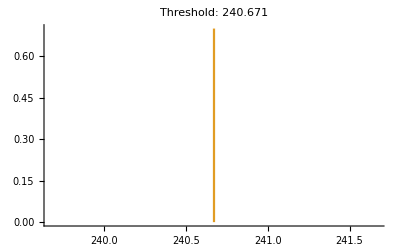

```mathematica
ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],0.7}}},PlotRange->{{280,290},All},Joined->True,PlotLabel->"Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

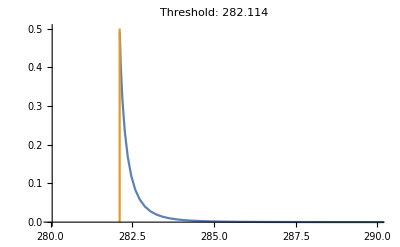

```mathematica
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],0.5}}},PlotRange->{{280,290},All},Joined->True,PlotLabel->"Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

### Debug

```mathematica
Block[{mQ=60},m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
ΦB[x_]=ϕxB;
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
ΦB[x_]=ϕxB;
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];]
```

Wavefunction build complete.

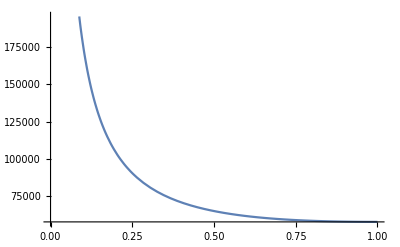

```mathematica
Plot[Sω1[ω1][M1,M2,M3,M4],{ω1,0,1}]
```

```mathematica
Block[{ω1=0.907479105147823,ω2,Sen},ω2=ω2p[ω1][M1,M2,M3,M4];Sen=√(Sω1[ω1][M1,M2,M3,M4]);If[ω2∈Reals&&Sen∈Reals,Print["ω1=",ω1,"    ω2=",ω2];{Sen,ℳone[ω1,ω2][M1][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω1=",ω1]]]
```

ω1=0.907479    ω2=0.708776

NIntegrate::ncvb: 在接近 {x,y} = {0.47396,0.589163} 处的 x 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 7087.77 和 143060..

NIntegrate::ncvb: 在接近 {x,y} = {0.526042,0.410879} 处的 x 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 7087.77 和 143060..

{244.244,-113404.}

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];𝒞[ℳ0[ω1,ω2]][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

0.09278

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];ℳ1[M1][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

NIntegrate::ncvb: 在接近 {x,y} = {0.47396,0.589163} 处的 x 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 7087.77 和 143060..

-56702.2

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,0,(ω1-ω2+x ω2)/ω1,1},Method->"PrincipalValue"],{x,0,1}])]
```

NIntegrate::pvrng: Singular points must be specified in the integration range in order to use PrincipalValue.

General::stop: Further output of NIntegrate::pvrng will be suppressed during this calculation.

NIntegrate::inumr: The integrand NIntegrate[((0.907479 0.907479) ϕ1((x 0.907479)/(1+0.907479-0.907479)) ϕ2(y) ϕ3(y 0.907479) ϕ4(x))/(Plus[«2»] 0.907479+Plus[«2»] 0.907479)^2,{y,0,1},Method→PrincipalValue] has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 1).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-4 NIntegrate[NIntegrate[(ϕ4(x) ϕ2(y) (ω1 ω2) ϕ3(y ω1) ϕ1((x ω2)/(-ω1+ω2+1)))/((1-x) ω2+(y-1) ω1)^2,{y,0,1},Method→PrincipalValue],{x,0,1}]

```mathematica
NI1[ω1_,ω2_][x_?NumberQ]:=NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,0,(ω1-ω2+x ω2)/ω1-λ}]
NI2[ω1_,ω2_][x_?NumberQ]:=NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,(ω1-ω2+x ω2)/ω1+λ,1}]
```

```mathematica
λ=10^-4;
```

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[NI1[ω1,ω2][x],{x,0,1}]+NIntegrate[NI2[ω1,ω2][x],{x,0,1}]-2/λ NIntegrate[ω1 ω2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}])]
```

$Aborted

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ NIntegrate[ω1 ω2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}])]
```

-1.12451×10^226-5.50215×10^104 ⅈ

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];Plot3D[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,1},PlotRange->{{0,1},{0,1},{0,10^6}}]]
```

-Graphics3D-

```mathematica
Block[{ω1=0.907479105147823,ω2,x=0.5,y,m=3},ω2=ω2p[ω1][M1,M2,M3,M4];y=(ω1-ω2+x ω2)/ω1-10^-m;(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x]]
```

3.35524×10^7

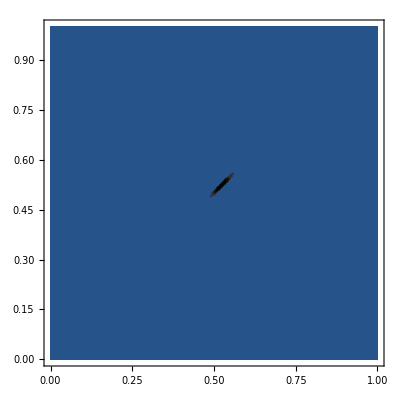

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];ContourPlot[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,1},PlotRange->All]]
```

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,(ω1-ω2+x ω2)/ω1-λ},Method->"MonteCarlo"])]
```

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 34135.2-4.63399×10^-37 ⅈ and 15577.3 for the integral and error estimates.

-136541.

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,(ω1-ω2+x ω2)/ω1+λ,1},Method->"AdaptiveMonteCarlo"])]
```

-14204.

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(-2/λ NIntegrate[ω1 ω2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}])]
```

25219.2

```mathematica
Table[Block[{ω1=0.907479105147823,ω2,x=0.45},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ ω1 ω2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x])],{λ,Table[10^-m,{m,0,10}]}]
```

NIntegrate::ncvb: 在接近 {y} = {0.44999999904303175292613841422061933173382093642533874344735522755} 处的 y 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 2.4418×10^8 和 1504.52.

NIntegrate::ncvb: 在接近 {y} = {0.45000000014934922506892608576000561741663045546568699961653692299} 处的 y 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 2.44179×10^8 和 1196.34.

{-7.57308130493703×10^559,-2.35687,-98.3352,-136.693,-447.685,-3550.47,-34577.6,-344848.,-3.44756×10^6,-3.44746×10^7,-3.44746×10^8}

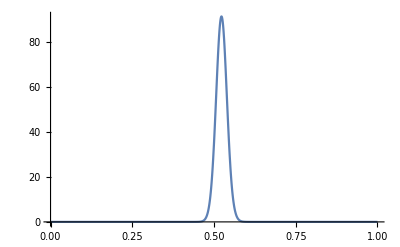

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];Plot[ ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1},PlotRange->All]]
```

```mathematica
Table[Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,λ,1-λ},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,λ,1-λ},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ NIntegrate[ω1 ω2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,λ,1-λ}])],{λ,Table[10^-m,{m,2,7,0.3}]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{448.803,-23.9047,-1064.14,-3188.95,-7453.27,-15974.1,-32981.7,-66919.3,-134635.,-269748.,-539339.,-1.07722×10^6,-2.15046×10^6,-4.29184×10^6,-8.56448×10^6,-1.70895×10^7,-3.40992×10^7}

```mathematica
Table[Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];((#+𝒮[#][ω1,ω2])&[If[1>ω1,-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ NIntegrate[ω1 ω2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}]),0]])],{λ,Table[10^-m,{m,0,10}]}]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

{-2.06510737652442×10^698,-60.1637-1.36561×10^104 ⅈ,406.722-2.22264×10^14 ⅈ,1632.58,11989.3,115365.,1.1491×10^6,1.14865×10^7,1.14864×10^8,1.1486×10^9,1.1486×10^10}

```mathematica
Plot3D[1/(x-y)^2,{x,0,1},{y,0,1}]
```

Power::infy: 碰到无穷表达式 1/0..

-Graphics3D-